## Tasks

1) get critical congestion code working (association)
2) post-processing : plots u, currents, m, ... 
	answers simple questions: boundary conditions,

```mathematica
BooleanConvert[a == 0 || b==0]
```

a==0||b==0

```mathematica
Names["MFGraphs`*"]
```

```mathematica
Get["MFGraphs`Examples`ExamplesData`"]
```

<|Vertices List→{1,2},Adjacency Matrix→{{0,1},{0,0}},Entrance Vertices and Currents→{{1,1}},Exit Vertices and Terminal Costs→{{2,2}},Switching Costs→{}|>

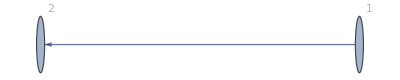
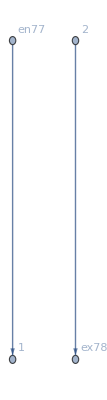
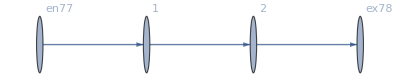
<|BG→-Graphics-,EntranceVertices→{1},InwardVertices→<|1→en77|>,InEdges→{en77->1},ExitVertices→{2},OutwardVertices→<|2→ex78|>,OutEdges→{2->ex78},AuxiliaryGraph→-Graphics-,FG→-Graphics-,VL→{1,2},EL→{1->2,2->ex78,en77->1},BEL→{1->2},FVL→{1,2,en77,ex78},AllTransitions→{{1,1->2,en77->1},{1,en77->1,1->2},{2,1->2,2->ex78},{2,2->ex78,1->2}},IncomingEdges→MFGraphs`Private`IncomingEdges$7605,OutgoingEdges→MFGraphs`Private`OutgoingEdges$7605,NoDeadEnds→{{1,1->2},{1,en77->1},{2,1->2},{2,2->ex78}},NoDeadStarts→{{2,1->2},{en77,en77->1},{1,1->2},{ex78,2->ex78}},jargs→{{2,1->2},{ex78,2->ex78},{1,en77->1},{1,1->2},{2,2->ex78},{en77,en77->1}},js→{j79,j80,j81,j82,j83,j84},jvars→<|{2,1->2}→j79,{ex78,2->ex78}→j80,{1,en77->1}→j81,{1,1->2}→j82,{2,2->ex78}→j83,{en77,en77->1}→j84|>,jts→{jt85,jt86,jt87,jt88},jtvars→<|{1,1->2,en77->1}→jt85,{1,en77->1,1->2}→jt86,{2,1->2,2->ex78}→jt87,{2,2->ex78,1->2}→jt88|>,uargs→{{1,1->2},{2,2->ex78},{en77,en77->1},{2,1->2},{ex78,2->ex78},{1,en77->1}},us→{u89,u90,u91,u92,u93,u94},uvars→<|{1,1->2}→u89,{2,2->ex78}→u90,{en77,en77->1}→u91,{2,1->2}→u92,{ex78,2->ex78}→u93,{1,en77->1}→u94|>,CurrentCompCon→MFGraphs`Private`CurrentCompCon$7605,EqCurrentCompCon→(j82==0||j79==0)&&(j83==0||j80==0)&&(j84==0||j81==0),TransitionCompCon→MFGraphs`Private`TransitionCompCon$7605,EqTransitionCompCon→(jt85==0||jt86==0)&&(jt87==0||jt88==0),Compu→MFGraphs`Private`Compu$7605,EqCompCon→jt85==0&&(jt86==0||-u89+u94==0)&&(jt87==0||-u90+u92==0)&&jt88==0,EqAllComp→(j82==0||j79==0)&&(j83==0||j80==0)&&(j84==0||j81==0)&&(jt85==0||jt86==0)&&(jt87==0||jt88==0)&&jt85==0&&(jt86==0||-u89+u94==0)&&(jt87==0||-u90+u92==0)&&jt88==0,EqPosCon→NonNegative[j79]&&NonNegative[j80]&&NonNegative[j81]&&NonNegative[j82]&&NonNegative[j83]&&NonNegative[j84]&&NonNegative[jt85]&&NonNegative[jt86]&&NonNegative[jt87]&&NonNegative[jt88],CurrentSplitting→MFGraphs`Private`CurrentSplitting$7605,CurrentGathering→MFGraphs`Private`CurrentGathering$7605,EqBalanceSplittingCurrents→j82==jt85&&j81==jt86&&j79==jt87&&j83==jt88,EqBalanceGatheringCurrents→j79==jt86&&j84==jt85&&j82==jt88&&j80==jt87,EntryArgs→{{1,en77->1}},EntryDataAssociation→<|{1,en77->1}→1|>,EqEntryIn→j81==1,NonZeroEntryCurrents→True,ExitCosts→<|ex78→2|>,ExitValues→MFGraphs`Private`ExitValues$7605,EqExitValues→u93==2,SwitchingCosts→<|{1,1->2,en77->1}→∞,{1,en77->1,1->2}→0,{2,1->2,2->ex78}→0,{2,2->ex78,1->2}→∞,{2,2->ex78,2->ex78}→∞,{2,2->ex78,en77->1}→∞,{1,en77->1,en77->1}→∞|>,OutRules→{{2,2->ex78,1->2}→∞,{2,2->ex78,2->ex78}→∞,{2,2->ex78,en77->1}→∞},InRules→{{1,1->2,en77->1}→∞,{1,en77->1,en77->1}→∞},Transu→MFGraphs`Private`Transu$7605,EqSwitchingConditions→u94≤u89&&u89≤∞&&u90≤∞&&u92≤u90,EqValue→MFGraphs`Private`EqValue$7605,EqValueAuxiliaryEdges→-u91+u94==0&&-u90+u93==0,EqAll→NonNegative[j79]&&NonNegative[j80]&&NonNegative[j81]&&NonNegative[j82]&&NonNegative[j83]&&NonNegative[j84]&&NonNegative[jt85]&&NonNegative[jt86]&&NonNegative[jt87]&&NonNegative[jt88]&&j82==jt85&&j81==jt86&&j79==jt87&&j83==jt88&&j79==jt86&&j84==jt85&&j82==jt88&&j80==jt87&&j81==1&&u93==2&&u94≤u89&&u89≤∞&&u90≤∞&&u92≤u90&&-u91+u94==0&&-u90+u93==0|>

```mathematica
n=26;
Data = DataG[n]
MFGEquations=DataToEquations[Data]
```

```mathematica
jays=AssociationThread[MFGEquations["BEL"],(MFGEquations["jvars"][AtHead[#]]-MFGEquations["jvars"][AtTail[#]]&)/@MFGEquations["BEL"]]
```

<|1->2→j79-j82|>

```mathematica
jaysInitial= #->0&/@MFGEquations["BEL"]//Association;
```

```mathematica
critialcongestionjays = 
Join[(MFGEquations["jvars"][AtHead[#]]-> 0)&/@MFGEquations["BEL"],(MFGEquations["jvars"][AtTail[#]]-> 0)&/@MFGEquations["BEL"]]
```

{j79→0,j82→0}

<|1->2→0|>

```mathematica
jays
```

```mathematica
Keys[MFGEquations]
```

{BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,FVL,AllTransitions,IncomingEdges,OutgoingEdges,NoDeadEnds,NoDeadStarts,jargs,js,jvars,jts,jtvars,uargs,us,uvars,CurrentCompCon,EqCurrentCompCon,TransitionCompCon,EqTransitionCompCon,Compu,EqCompCon,EqAllComp,EqPosCon,CurrentSplitting,CurrentGathering,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EntryArgs,EntryDataAssociation,EqEntryIn,NonZeroEntryCurrents,ExitCosts,ExitValues,EqExitValues,SwitchingCosts,OutRules,InRules,Transu,EqSwitchingConditions,EqValue,EqValueAuxiliaryEdges,EqAll}

```mathematica
(*here is where we are developing the world association!!!*)
```

```mathematica
world=Association[{"EqAll"->MFGEquations["EqAll"],"EqAllComp"->MFGEquations["EqAllComp"],
"edges"->  MFGEquations["BEL"],"lhs"->Association[(#->MFGEquations["uvars"][AtHead[#]]-MFGEquations["uvars"][AtTail[#]]-jays[#]&)/@MFGEquations["BEL"]],"rhs"->Association[(#->-jays[#]&)/@MFGEquations["BEL"]]}]
```

<|EqAll→NonNegative[j79]&&NonNegative[j80]&&NonNegative[j81]&&NonNegative[j82]&&NonNegative[j83]&&NonNegative[j84]&&NonNegative[jt85]&&NonNegative[jt86]&&NonNegative[jt87]&&NonNegative[jt88]&&j82==jt85&&j81==jt86&&j79==jt87&&j83==jt88&&j79==jt86&&j84==jt85&&j82==jt88&&j80==jt87&&j81==1&&u93==2&&u94≤u89&&u89≤∞&&u90≤∞&&u92≤u90&&-u91+u94==0&&-u90+u93==0,EqAllComp→(j82==0||j79==0)&&(j83==0||j80==0)&&(j84==0||j81==0)&&(jt85==0||jt86==0)&&(jt87==0||jt88==0)&&jt85==0&&(jt86==0||-u89+u94==0)&&(jt87==0||-u90+u92==0)&&jt88==0,edges→{1->2},lhs→<|1->2→-j79+j82-u89+u92|>,rhs→<|1->2→-j79+j82|>|>

```mathematica
world/.critialcongestionjays
```

<|EqAll→NonNegative[0]&&NonNegative[j80]&&NonNegative[j81]&&NonNegative[0]&&NonNegative[j83]&&NonNegative[j84]&&NonNegative[jt85]&&NonNegative[jt86]&&NonNegative[jt87]&&NonNegative[jt88]&&0==jt85&&j81==jt86&&0==jt87&&j83==jt88&&0==jt86&&j84==jt85&&0==jt88&&j80==jt87&&j81==1&&u93==2&&u94≤u89&&u89≤∞&&u90≤∞&&u92≤u90&&-u91+u94==0&&-u90+u93==0,EqAllComp→(0==0||0==0)&&(j83==0||j80==0)&&(j84==0||j81==0)&&(jt85==0||jt86==0)&&(jt87==0||jt88==0)&&jt85==0&&(jt86==0||-u89+u94==0)&&(jt87==0||-u90+u92==0)&&jt88==0,edges→{1->2},lhs→<|1->2→-0+0-u89+u92|>,rhs→<|1->2→-0+0|>|>

```mathematica
critialcongestionjays
```

{j79-j82→0}

```mathematica
Keys[world]
```

{EqAll,EqAllComp,edges,lhs,rhs}

```mathematica
G[world_Association]:=Function[jays,Module[{numericworld = world,AssembledEquations},
numericworld = numericworld/. jays;
AssembledEquations=And@@Map[((numericworld["lhs"][#]==numericworld["rhs"][#]))&,numericworld["edges"]]
(*TODO solve and do all the things diogo said.*)]]
```

```mathematica
jays
```

<|1->2→j79-j82|>

```mathematica
jays/.critialcongestionjays
```

<|1->2→0-0|>

```mathematica
G[world][jays/.critialcongestionjays]
```

-j79+j82-u89+u92==-j79+j82

```mathematica
(G[world][gsgsgsg])
```

-j79+j82-u89+u92==-j79+j82